```mathematica
e=1;
m=5;
P=2^m;
Ep=500;
c$=Table[0,{i,1,Ep}];
cMG=Table[0,{i,1,Ep}];
cBG=Table[0,{i,1,Ep}];
```

```mathematica
(Label[New];
n1=1;"$ player";
n2=1;"MG player";
n3=99;"Back ground";
n=n1+n2+n3;
T=399;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[P-1];
mu⟦2⟧=RandomInteger[P-1];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
nM=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,n},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=10;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
c=Table[100,{i,1,n}];
NStock=Table[9,{i,1,n},{i,1,2}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
Tinfor=Table[0,{i,1,P}];
Onetimes=Table[0,{i,1,P}];
CondionPinfor=Table[0,{i,1,P}];
BScollect=Table[0,{i,1,n}];
"initial set";
Do[
Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^P-1}],2,P]];
Do[Action⟦1,k⟧=(2*Action⟦1,k⟧-1),{k,1,P}];
RandomStrategy=Action;
AgentStrategy⟦i,s⟧=Flatten[RandomStrategy,1],{s,1,S},{i,1,n}]
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
Label[begin];
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
If[OddQ[t],Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n1}];
Do[If[BS⟦i,1⟧==AgentStrategy⟦i,1⟧,BScollect⟦i⟧=BScollect⟦i⟧+1,BScollect⟦i⟧=BScollect⟦i⟧-1],{i,1,n1}];,
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}]];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
nM⟦t⟧=(nM⟦t-1⟧+(-A⟦t-1⟧));
"signal=UnitStep[MarketAction]";
"Price/Cash/Wealth update deal t+1 ";
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧);
If[t==3,Do[c⟦i⟧=100,{i,1,n}];
Do[NStock⟦i,2⟧=9,{i,1,n}];,Do[c⟦i⟧=c⟦i⟧-BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧);
c⟦i⟧=N[c⟦i⟧],{i,1,n}];
Do[NStock⟦i,1⟧=NStock⟦i,2⟧;
NStock⟦i,2⟧=NStock⟦i,1⟧+BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,n}];
];
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";
If[OddQ[t],Do[PayoffFunction⟦i,s⟧=0,{s,1,S},{i,1,n1}];,
Do[PayoffFunction⟦i,s⟧=(AgentStrategy⟦i,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S},{i,1,n1}];]
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";
If[t>T,Goto[sample],Goto[begin]];
Label[sample];
c$⟦e⟧=c⟦1⟧;
cMG⟦e⟧=c⟦2⟧;
cBG⟦e⟧=Mean[c⟦3;;n⟧];
e=e+1;
If[e>Ep,Break,Goto[New]];)//AbsoluteTiming
```

{1194.1633,Null}

```mathematica
1191/60//N
```

19.85

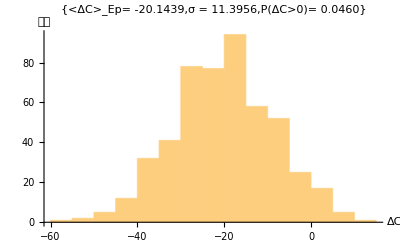

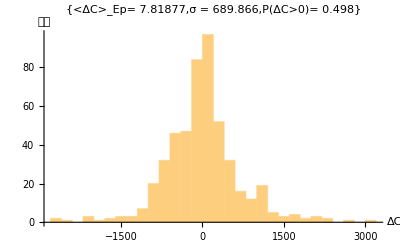

```mathematica
Histogram[c$-100,AxesLabel->{ΔC,次數},PlotLabel->{ "<ΔC>_Ep= "<>ToString[Mean[c$-100]],"σ = "<>ToString[StandardDeviation[c$-100]],"P(ΔC>0)= "<>ToString[N[1/Ep Total[UnitStep[c$-100]],3]]}]
Histogram[cMG-100,AxesLabel->{ΔC,次數},PlotLabel-> {"<ΔC>_Ep= "<>ToString[Mean[cMG-100]],"σ = "<>ToString[StandardDeviation[cMG-100]],"P(ΔC>0)= "<>ToString[N[1/Ep Total[UnitStep[cMG-100]],3]]}]
```

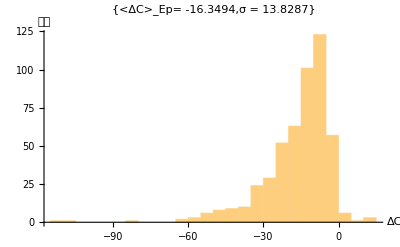

```mathematica
Histogram[cBG-100,AxesLabel->{ΔC,次數},PlotLabel->{ "<ΔC>_Ep= "<>ToString[Mean[cBG-100]],"σ = "<>ToString[StandardDeviation[cBG-100]]}]
```

```mathematica
Sum[A⟦t⟧*Price⟦t⟧,{t,1,T}]//N
```

-1658.47

```mathematica
-14.46*99
```

-1431.54

```mathematica
Sum[1/(√n)(A⟦t⟧)^2,{t,1,T}]//N
```

2423.61